```mathematica
A = {
{5, -9, -7, 1}, 
{-9, 5, -1, 7},
{-7, -1, 5, 9},
{1, 7, 9, 5}
};

B = {{3}, {3}, {1}, {3}};

c = {
{2, -2, 2, 2}, 
{-2, 4, 2, 4}
};

QI=IdentityMatrix[4]; nu = 1; R = {{1}}; 
aK3 = 4;
aL3= 12;
```

```mathematica
{P,Aj}=JordanDecomposition[A];
{Bj,Cj}={Inverse[P].B,c.P};
```

```mathematica
(*Набор 3, синтез K3*)

tildeAaK3=A+aK3 QI;
PaK3=Round[RiccatiSolve[{tildeAaK3,B},{QI,R/nu}],0.01]//N
K3=Round[-Inverse[R].Transpose[B].PaK3 ,0.01]//N
AclaK3 = A + B.K3;Eigenvalues[Round[AclaK3,0.01]]// N
```

{{621.17,-871.94,338.83,88.03},{-871.94,1239.82,-503.63,-135.78},{338.83,-503.63,236.62,71.73},{88.03,-135.78,71.73,24.07}}

{{149.39,-192.67,42.59,-0.69}}

{-27.2317,-17.8588,-12.2295,-12.}

```mathematica
(*Набор 3, синтез L3*)

Lj3={{0,0},{0.,9.8361},{-2.5492,0.},{0.,-7.4105}};
L3=Round[N[P.Lj3],0.01]

AclaK3=A+L3.c;
Eigenvalues[N[AclaK3]]
```

{{-2.55,17.25},{2.55,2.43},{-2.55,-17.25},{-2.55,2.43}}

{-12.78+18.6599 ⅈ,-12.78-18.6599 ⅈ,-12.4+0. ⅈ,-12.+0. ⅈ}

```mathematica
BK=B.K3;LC=L3.c;system={x1'[t]==A[[1,1]]*x1[t]+A[[1,2]]*x2[t]+A[[1,3]]*x3[t]+A[[1,4]]*x4[t]+BK[[1,1]]*x5[t]+BK[[1,2]]*x6[t]+BK[[1,3]]*x7[t]+BK[[1,4]]*x8[t],x2'[t]==A[[2,1]]*x1[t]+A[[2,2]]*x2[t]+A[[2,3]]*x3[t]+A[[2,4]]*x4[t]+BK[[2,1]]*x5[t]+BK[[2,2]]*x6[t]+BK[[2,3]]*x7[t]+BK[[2,4]]*x8[t],x3'[t]==A[[3,1]]*x1[t]+A[[3,2]]*x2[t]+A[[3,3]]*x3[t]+A[[3,4]]*x4[t]+BK[[3,1]]*x5[t]+BK[[3,2]]*x6[t]+BK[[3,3]]*x7[t]+BK[[3,4]]*x8[t],x4'[t]==A[[4,1]]*x1[t]+A[[4,2]]*x2[t]+A[[4,3]]*x3[t]+A[[4,4]]*x4[t]+BK[[4,1]]*x5[t]+BK[[4,2]]*x6[t]+BK[[4,3]]*x7[t]+BK[[4,4]]*x8[t],x5'[t]==(A[[1,1]]+BK[[1,1]])*x5[t]+(A[[1,2]]+BK[[1,2]])*x6[t]+(A[[1,3]]+BK[[1,3]])*x7[t]+(A[[1,4]]+BK[[1,4]])*x8[t]+LC[[1,1]]*(x5[t]-x1[t])+LC[[1,2]]*(x6[t]-x2[t])+LC[[1,3]]*(x7[t]-x3[t])+LC[[1,4]]*(x8[t]-x4[t]),x6'[t]==(A[[2,1]]+BK[[2,1]])*x5[t]+(A[[2,2]]+BK[[2,2]])*x6[t]+(A[[2,3]]+BK[[2,3]])*x7[t]+(A[[2,4]]+BK[[2,4]])*x8[t]+LC[[2,1]]*(x5[t]-x1[t])+LC[[2,2]]*(x6[t]-x2[t])+LC[[2,3]]*(x7[t]-x3[t])+LC[[2,4]]*(x8[t]-x4[t]),x7'[t]==(A[[3,1]]+BK[[3,1]])*x5[t]+(A[[3,2]]+BK[[3,2]])*x6[t]+(A[[3,3]]+BK[[3,3]])*x7[t]+(A[[3,4]]+BK[[3,4]])*x8[t]+LC[[3,1]]*(x5[t]-x1[t])+LC[[3,2]]*(x6[t]-x2[t])+LC[[3,3]]*(x7[t]-x3[t])+LC[[3,4]]*(x8[t]-x4[t]),x8'[t]==(A[[4,1]]+BK[[4,1]])*x5[t]+(A[[4,2]]+BK[[4,2]])*x6[t]+(A[[4,3]]+BK[[4,3]])*x7[t]+(A[[4,4]]+BK[[4,4]])*x8[t]+LC[[4,1]]*(x5[t]-x1[t])+LC[[4,2]]*(x6[t]-x2[t])+LC[[4,3]]*(x7[t]-x3[t])+LC[[4,4]]*(x8[t]-x4[t]), x1[0]==1,x2[0]==1,x3[0]==1,x4[0]==1,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0};

sol=NDSolve[system,{x1,x2,x3,x4,x5,x6,x7,x8},{t,0,5}];

x1true[t_]:=x1[t]/.sol; x1hat[t_]:=x5[t]/.sol;
x2true[t_]:=x2[t]/.sol; x2hat[t_]:=x6[t]/.sol;
x3true[t_]:=x3[t]/.sol; x3hat[t_]:=x7[t]/.sol;
x4true[t_]:=x4[t]/.sol; x4hat[t_]:=x8[t]/.sol;

e1[t_]=x1true[t]-x1hat[t];
e2[t_]=x2true[t]-x2hat[t];
e3[t_]=x3true[t]-x3hat[t];
e4[t_]=x4true[t]-x4hat[t];
```

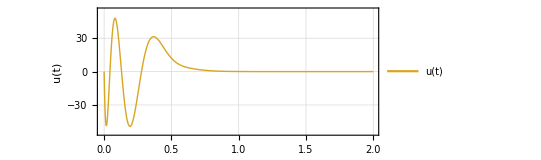

```mathematica
(*Управление*)

u[t_]:=K3[[1,1]]*x5[t]+K3[[1,2]]*x6[t]+K3[[1,3]]*x7[t]+K3[[1,4]]*x8[t]/.sol;

U3 = Plot[u[t],{t,0,2},PlotStyle->{RGBColor[0.85,0.65,0.13],Thick},PlotLegends->Placed[LineLegend[{"u(t)"},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.87,0.9}],PlotRange->{{-0.01,2},{-55,55}}, Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic, GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task2/U3.pdf"}],U3];
```

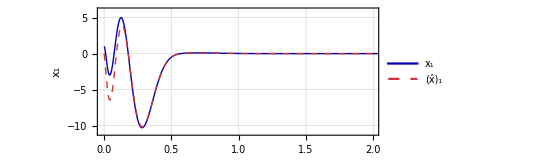

```mathematica
(*2. Сравнение x(t) и x_hat(t)*)

xx1=Plot[{x1true[t],x1hat[t]},{t,0,5},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0.8,0.2,0.2],Dashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[OverHat[x],1]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->17}],{0.73,0.89}],PlotRange->{{-0.01,2},{-11,6}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->17],Style[Subscript[x,1],FontFamily->"Times New Roman",FontSize->17]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4, BaseStyle->{FontSize->12}]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task2/xx31.pdf"}],xx1];
```

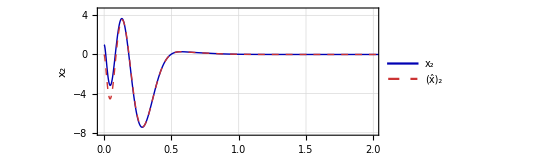

```mathematica
xx2=Plot[{x2true[t],x2hat[t]},{t,0,5},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0.8,0.2,0.2],Dashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,2],Subscript[OverHat[x],2]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->17}],{0.73,0.89}],PlotRange->{{-0.01,2},{-8,4.5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->17],Style[Subscript[x,2],FontFamily->"Times New Roman",FontSize->17]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4, BaseStyle->{FontSize->12}]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task2/xx32.pdf"}],xx2];
```

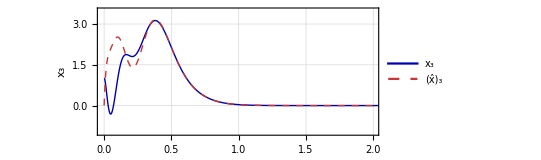

```mathematica
xx3=Plot[{x3true[t],x3hat[t]},{t,0,5},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0.8,0.2,0.2],Dashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,3],Subscript[OverHat[x],3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->17}],{0.73,0.89}],PlotRange->{{-0.01,2},{-1,3.5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->17],Style[Subscript[x,3],FontFamily->"Times New Roman",FontSize->17]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4, BaseStyle->{FontSize->12}]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task2/xx33.pdf"}],xx3];
```

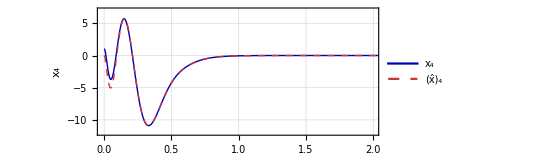

```mathematica
xx4=Plot[{x4true[t],x4hat[t]},{t,0,5},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0.8,0.2,0.2],Dashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,4],Subscript[OverHat[x],4]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->17}],{0.73,0.89}],PlotRange->{{-0.01,2},{-12,7}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->17],Style[Subscript[x,4],FontFamily->"Times New Roman",FontSize->17]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4, BaseStyle->{FontSize->12}]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task2/xx34.pdf"}],xx4];
```

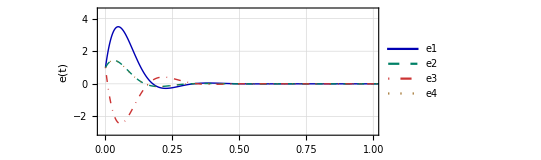

```mathematica
(*3. Ошибка наблюдения e(t)=x(t)-x_hat(t)*)

e=Plot[{e1[t],e2[t],e3[t],e4[t]},{t,0,2},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick},{RGBColor[0.6,0.4,0.1],Dotted,Thick}},PlotLegends->Placed[LineLegend[{"e1","e2","e3","e4"},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.55,0.92}],PlotRange->{{-0.01,1},{-3,4.5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["e(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task2/e3.pdf"}],e];
```